## Chaotic trajectories

Find an appropriate map for the Lorenz attractor to the 8x8 beatpad region that will hopefully generate reasonable results

https://highfellow.github.io/lorenz-attractor/attractor.html

For this we will ultimately be simulating the Lorenz attractor in js (for the website) and in c++ (for the chaos sampler)

```mathematica
(*Define the Lorenz system parameters*)σ=10;
ρ=28;
β=2.3;

(*Define the Lorenz system of differential equations*)
lorenzEquations={x'[t]==σ (y[t]-x[t]),y'[t]==x[t] (ρ-z[t])-y[t],z'[t]==x[t] y[t]-β z[t],x[0]==1,y[0]==1,z[0]==1};

(*Solve the differential equations using NDSolve*)
solution=NDSolve[lorenzEquations,{x,y,z},{t,0,1000}];

(*Plot the Lorenz attractor trajectory*)
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/. solution],{t,0,100},PlotRange->All,AxesLabel->{"x","y","z"},PlotStyle->{Blue,Thick},BoxRatios->{1,1,0.7},ImageSize->Large,Ticks->None]
```

-Graphics3D-

```mathematica
solution
```

{{x→InterpolatingFunction[{{0., 1000.}}, <>],y→InterpolatingFunction[{{0., 1000.}}, <>],z→InterpolatingFunction[{{0., 1000.}}, <>]}}

Apply a linear transformation to these points in order to plot them

```mathematica
points3d = Table[Evaluate[{x[t],y[t],z[t]}/. solution][[1]],{t,100,1000,0.01}];
```

```mathematica
points2d = Table[{point.{0,0,1},point.{1,1,0}},{point,points3d}];
```

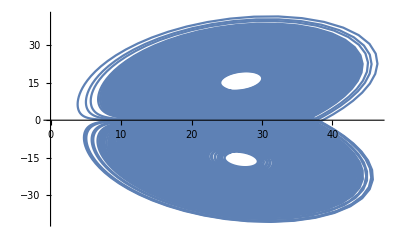

```mathematica
ListLinePlot[points2d]
```

Now that we have these trajectories we can start to assign samples to labels.

The steps in our process are going to first be to load a sample which has been chopped up by running a trajectory. (Honestly we are first going to run a trajectory for a while to get rid of the transients.

```mathematica
points2dNorm = Transpose[{(points2d[[;;,1]]-Min[points2d[[;;,1]]])/(Max[points2d[[;;,1]]]-Min[points2d[[;;,1]]]),(points2d[[;;,2]]-Min[points2d[[;;,2]]])/(Max[points2d[[;;,2]]]-Min[points2d[[;;,2]]])}];
```

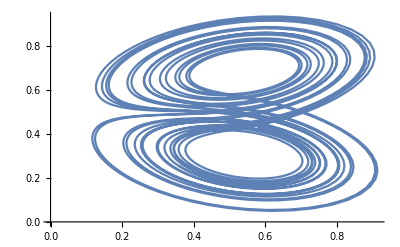

```mathematica
ListLinePlot[points2dNorm[[;;2500]]]
```

```mathematica
Mod[6-1,3]+1
```

3

```mathematica
assignmentRes = 64;
```

```mathematica
sampleLength=32;
```

```mathematica
eps = 0.001;
```

```mathematica
assignments=ConstantArray[-1,{assignmentRes,assignmentRes}];
Do[assignments[[Ceiling[(1-eps)*points2dNorm[[t,1]]*assignmentRes+eps],Ceiling[(1-eps)*points2dNorm[[t,2]]*assignmentRes+eps]]]=Mod[t-1,sampleLength]+1;,{t,1,Length[points2dNorm]}]
```

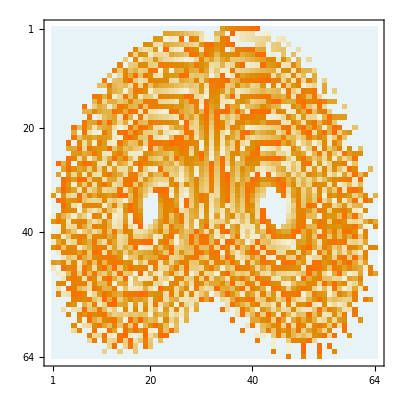

```mathematica
assignments//MatrixPlot
```

```mathematica
Table[assignments[[Ceiling[(1-eps)*points2dNorm[[t,1]]*assignmentRes+eps],Ceiling[(1-eps)*points2dNorm[[t,2]]*assignmentRes+eps]]],{t,1,Length[points2dNorm]}]
```

In reality, we could be subsampling the grid at a much finer resolution. Colors represent where in the sample we are actually drawing from. When the button is pressed we show the visual but th